### Aufgabe 2.1.1

```mathematica
f[t_]:=a*t^3+b*t^2+c*t+d
```

```mathematica
Solve[f[5]==35&&f[10]==45&&f'[10]==0&&f[15]==f[10]-7.5]
```

{{a→0.01,b→-0.65,c→10.,d→-1.69864×10^-14}}

```mathematica
g[t_]:=0.01*t^3-0.65*t^2+10*t+0
```

### Aufgabe 2.1.2

Das Auto bewegt sich im nehativen Bereich das ist doof .

### Aufgbae 2.2.1

```mathematica
v[t_]:=3.3*t^2*E^(-0.2*t)
```

```mathematica
Integrate[v[t],{t,0,40}]/40
```

20.3413

### Aufgabe 2.2.2

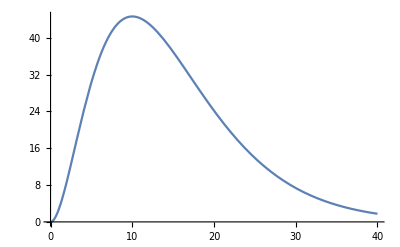

```mathematica
Plot[v[t],{t,0,40}]
```

```mathematica
v[10]
```

44.6606

```mathematica
Solve[v[t]==22]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-2.09415},{t→3.76085},{t→20.9228}}

```mathematica
Integrate[v[t],{t,0,20.9228}]
```

649.862

### Aufgabe 2.3